```mathematica
(*Fonctions*)
```

```mathematica
NLegendre[n_,m_,x_]:=Sqrt[Factorial[n-m]*(2n+1)/(2*Factorial[n+m])]*LegendreP[n,m,x];
```

```mathematica
hI[α_,m_,l_,n_]:=NIntegrate[((1-ξ)/2)^α*NLegendre[l,m,ξ]*NLegendre[n,m,ξ],{ξ,-1,1}]
hJ[α_,m_,l_,n_]:=NIntegrate[((1-ξ)/2)^α*((1+ξ)/2)^(-1)*NLegendre[l,m,ξ]*NLegendre[n,m,ξ],{ξ,-1,1}]
```

```mathematica
(*Parameters*)
```

```mathematica
m=2;
ϵ=0.2;
Nbasis=30;
```

```mathematica
(*Matrix elements*)
```

```mathematica
Aln[m_,l_,n_]:=m*Sqrt[1-ϵ]*hI[3/4,m,l,n];
Bln[m_,l_,n_]:=If[l>m,(1/2)*(Sqrt[(2l+1)(l+m+1)(l-m+1)/(2l+3)]*hJ[3/4,m,l+1,n]+hJ[3/4,m,l,n]-Sqrt[(2l+1)(l+m)(l-m)/(2l-1)]*hJ[3/4,m,l-1,n]),(1/2)*(Sqrt[(2l+1)(l+m+1)(l-m+1)/(2l+3)]*hJ[3/4,m,l+1,n]+hJ[3/4,m,l,n])];
Cln[m_,l_,n_]:=m*hJ[3/4,m,l,n];
Dln[m_,l_,n_]:=If[n>m,(1/2)(1/(2n+1)-ϵ/3)*(-Sqrt[(2n+1)(n+m+1)(n-m+1)/(2n+3)]*hI[3/4,m,l,n+1]-hI[3/4,m,l,n]+Sqrt[(2n+1)(n+m)(n-m)/(2n-1)]*hI[3/4,m,l,n-1]),(-Sqrt[(2n+1)(n+m+1)(n-m+1)/(2n+3)]*hI[3/4,m,l,n+1]-hI[3/4,m,l,n])];
Fln[m_,l_,n_]:=2*Sqrt[1-ϵ]*hI[3/4,m,l,n];
Gln[m_,l_,n_]:=-m(1/(2n+1)-ϵ/3)*hI[3/4,m,l,n];
Hln[m_,l_,n_]:=(1/2)*Sqrt[1-ϵ]*(hI[3/4,m,l,n]+3*hI[7/4,m,l,n]);
```

```mathematica
(*Complete matrix*)
```

```mathematica
Mln=ConstantArray[0,{3(Nbasis+1),3(Nbasis+1)}];
For[l=m,l≤m+Nbasis,l++,
For[n=m,n≤m+Nbasis,n++,
(*Aln*)
Mln[[l-m+1,n-m+1]]=Aln[m,l,n];
(*Bln*)
Mln[[l-m+1,n-m+1+(Nbasis+1)]]=Bln[m,l,n];
(*Cln*)
Mln[[l-m+1,n-m+1+2(Nbasis+1)]]=Cln[m,l,n];
(*Dln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1]]=Dln[m,l,n];
(*Aln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1+(Nbasis+1)]]=Aln[m,l,n];
(*Fln*)
Mln[[(Nbasis+1)+l-m+1,n-m+1+2(Nbasis+1)]]=Fln[m,l,n];
(*Gln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1]]=Gln[m,l,n];
(*Hln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1+(Nbasis+1)]]=Hln[m,l,n];
(*Aln*)
Mln[[2(Nbasis+1)+l-m+1,n-m+1+2(Nbasis+1)]]=Aln[m,l,n];
]

]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.998382637986487545163349910382066809688694775104522705078125}. NIntegrate obtained 4.75265×10^-8 and 3.97277×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.998382637986487545163349910382066809688694775104522705078125}. NIntegrate obtained 3.31944×10^-8 and 3.67514×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.843781}. NIntegrate obtained 2.36031×10^-8 and 2.83837×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
LiEgv=Eigenvalues[Mln]
```

{8.68215+0.295395 ⅈ,8.68215-0.295395 ⅈ,7.04003+0. ⅈ,6.72874+0. ⅈ,5.75228+0. ⅈ,5.29242+0. ⅈ,-4.90128+0.505157 ⅈ,-4.90128-0.505157 ⅈ,4.64502+0. ⅈ,4.16867+0. ⅈ,3.68296+0. ⅈ,-3.38696+0.327201 ⅈ,-3.38696-0.327201 ⅈ,3.2271+0. ⅈ,2.82374+0. ⅈ,1.7782+1.77425 ⅈ,1.7782-1.77425 ⅈ,2.40935+0. ⅈ,-2.29237+0.213252 ⅈ,-2.29237-0.213252 ⅈ,2.25239+0. ⅈ,1.66371+1.45847 ⅈ,1.66371-1.45847 ⅈ,0.95172+1.92367 ⅈ,0.95172-1.92367 ⅈ,1.96503+0.0493611 ⅈ,1.96503-0.0493611 ⅈ,1.52575+1.12691 ⅈ,1.52575-1.12691 ⅈ,1.85625+0.0259699 ⅈ,1.85625-0.0259699 ⅈ,1.8137+0. ⅈ,1.74684+0.0360135 ⅈ,1.74684-0.0360135 ⅈ,1.68288+0. ⅈ,1.60536+0.0562816 ⅈ,1.60536-0.0562816 ⅈ,1.34611+0.83541 ⅈ,1.34611-0.83541 ⅈ,1.50256+0. ⅈ,-1.45809+0.129626 ⅈ,-1.45809-0.129626 ⅈ,1.44287+0.0652687 ⅈ,1.44287-0.0652687 ⅈ,1.30975+0.073604 ⅈ,1.30975-0.073604 ⅈ,1.27666+0. ⅈ,1.14116+0.562636 ⅈ,1.14116-0.562636 ⅈ,1.10971+0.0282174 ⅈ,1.10971-0.0282174 ⅈ,1.02517+0. ⅈ,0.928843+0.355579 ⅈ,0.928843-0.355579 ⅈ,0.884338+0.0592478 ⅈ,0.884338-0.0592478 ⅈ,-0.824209+0.0625455 ⅈ,-0.824209-0.0625455 ⅈ,0.824938+0. ⅈ,0.728179+0.192332 ⅈ,0.728179-0.192332 ⅈ,0.684188+0.0640973 ⅈ,0.684188-0.0640973 ⅈ,0.625365+0. ⅈ,0.527182+0.0936867 ⅈ,0.527182-0.0936867 ⅈ,0.508218+0.0368393 ⅈ,0.508218-0.0368393 ⅈ,0.440086+0. ⅈ,-0.392298+0. ⅈ,0.371033+0.072113 ⅈ,0.371033-0.072113 ⅈ,0.358067+0. ⅈ,-0.339715+0. ⅈ,0.294259+0. ⅈ,0.272302+0.049491 ⅈ,0.272302-0.049491 ⅈ,0.225683+0. ⅈ,0.191201+0.0266651 ⅈ,0.191201-0.0266651 ⅈ,0.164046+0. ⅈ,0.123096+0.0146252 ⅈ,0.123096-0.0146252 ⅈ,-0.109458+0. ⅈ,0.108619+0. ⅈ,0.0727604+0.00601668 ⅈ,0.0727604-0.00601668 ⅈ,0.0571655+0. ⅈ,0.0461364+0. ⅈ,-0.0460171+0. ⅈ,0.035037+0. ⅈ,0.0281493+0. ⅈ,0.0156108+0. ⅈ}

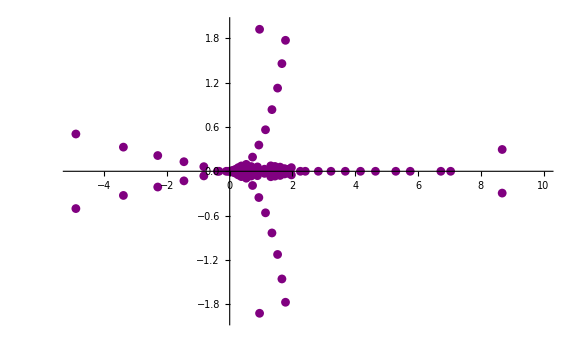

```mathematica
LiEgvRe=Re[LiEgv];
LiEgvIm=Im[LiEgv];
LiEgv2D={LiEgvRe,LiEgvIm}//Transpose;
ListPlot[LiEgv2D,PlotRange->{{-5,10},{-2,2}},PlotStyle->Purple,ImageSize->Large]
```

```mathematica
Mln[[3(25+1),3(25+1)]]
```

1.05758

```mathematica
Mln[[2(30+1)+17,(30+1)+12]]
```

-0.000502198

```mathematica
Fln[m,m,m]
```

1.1115

```mathematica
hI[3/4+1,m-1,m-1+24,m-1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {-0.839875}. NIntegrate obtained 2.07124×10^-8 and 1.51685×10^-11 for the integral and error estimates.

2.07124×10^-8